```mathematica
(*
Physics Discord:
[9:36 PM] thinking:http://www.skywatcherusa.com/product-category/telescopes/dobsonians/
[9:37 PM] thinking:https://www.highpointscientific.com/brands/apertura
[9:37 PM] thinking:https://www.telescope.com/Telescopes/Dobsonian-Telescopes/pc/1/12.uts
[9:38 PM] thinking:https://www.meade.com/lightbridge-telescopes.html
*)
```

```mathematica
scopesSWU={{6,285},{8,370},{10,545},{12,1015},{14,2305},{16,2950},{18,5499},{20,6499}};
scopesHPS={{8,450},{10,650},{12,880}};
scopesTS={{4.5,230},{6,270},{8,286},{10,496},{12,1050},{14,1900},{16,3700}};
scopesM={{10,699},{12,999},{16,1999}};
```

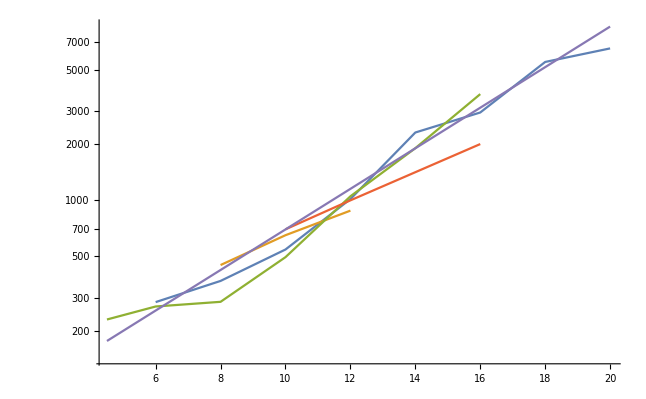

```mathematica
ListLogPlot[{scopesSWU,scopesHPS,scopesTS,scopesM,{#,200Exp[.25(#-5)]}&/@{4.5,6,8,10,12,14,16,18,20}},Joined->True]
```

```mathematica
Map[{#[[1]],#[[2]]-200}&,{scopesSWU,scopesHPS,scopesTS,scopesM},{2}]
```

{{{6,85},{8,170},{10,345},{12,815},{14,2105},{16,2750},{18,5299},{20,6299}},{{8,250},{10,450},{12,680}},{{4.5,30},{6,70},{8,86},{10,296},{12,850},{14,1700},{16,3500}},{{10,499},{12,799},{16,1799}}}

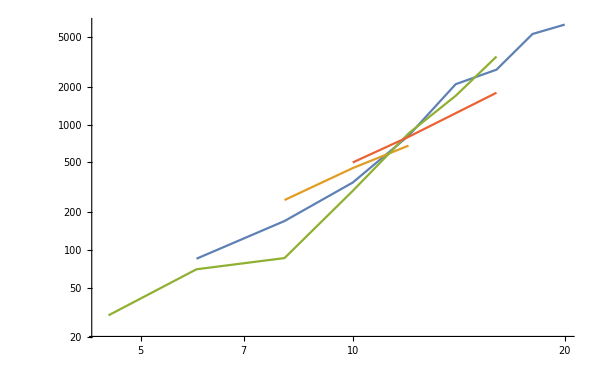

```mathematica
ListLogLogPlot[Map[{#[[1]],#[[2]]-200}&,{scopesSWU,scopesHPS,scopesTS,scopesM},{2}],Joined->True]
```

```mathematica
Log[6299/30]/Log[20/4.5]
```

3.58458

```mathematica
Log[2]/.25
```

2.77259